### Functions

```mathematica
preFactor = 2.680594*^-08;
```

### The limiting expression for Barbosa

```mathematica
nFacRBInf[phiBar_]:=1/2(Exp[phiBar] Erfc[√phiBar])+√(phiBar/π)
```

```mathematica
funkerLiemohn[Ep_,Tm_,Kmeas_]:=Kmeas/preFactor * √Tm *nFacRBInf[Ep/Tm];
```

```mathematica
funkerLiemohn[945,110,measCond]
```

0.669802

```mathematica
N[nFacRBInf[Ep/Tm]]
```

1.74507

### Condiciones

```mathematica
(*for using characteristic energy*)
(*Ep = 1075;*)
(*measCond = 1.40*^-9;*)
```

```mathematica
(*for using peak energy*)
Ep = 945;
Tm=110;
measCond = 9.81*^-10;
```

```mathematica
minDens=1.73;
maxDens=2.07;
minT=73.14;
maxT= 153.68;
```

## FINALE

```mathematica
kappas={1.55,1.6,1.75,2,2.45,4,10,1000};
```

```mathematica
tick = 0.002;
```

```mathematica
grayLev1=0.4;
grayLev2=0.6;
```

```mathematica
fontSize=19;
xScaled = 0.94;
```

```mathematica
styles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev1],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Black,Thickness[tick]]};
```

```mathematica
placeList={Below,Below,Below,Below,Below,Below,Below,Below,Below};
```

```mathematica
nDigs={3,3,3,3,3,3,3,3,3};
```

```mathematica
kapStrVals=Table[NumberForm[kappas[[k]],nDigs[[k]]],{k,1,8}];
```

```mathematica
kapStrVals[[5]] = StringForm["κ_t (≃ 2.45)"];
```

```mathematica
kappaLabels=Table[StringForm["κ = `1`",kapStrVals[[k]]],{k,1,8}]
```

{κ = 1.55,κ = 1.6,κ = 1.75,κ = 2,κ = κ_t (≃ 2.45),κ = 4,κ = 10,κ = 1000}

```mathematica
kappaLabels[[8]]=StringForm[" "];
```

## Just Maxwellian (and true Maxwellian, by the Way)

```mathematica
funkerLiemohn[Ep,110,measCond]
```

0.669802

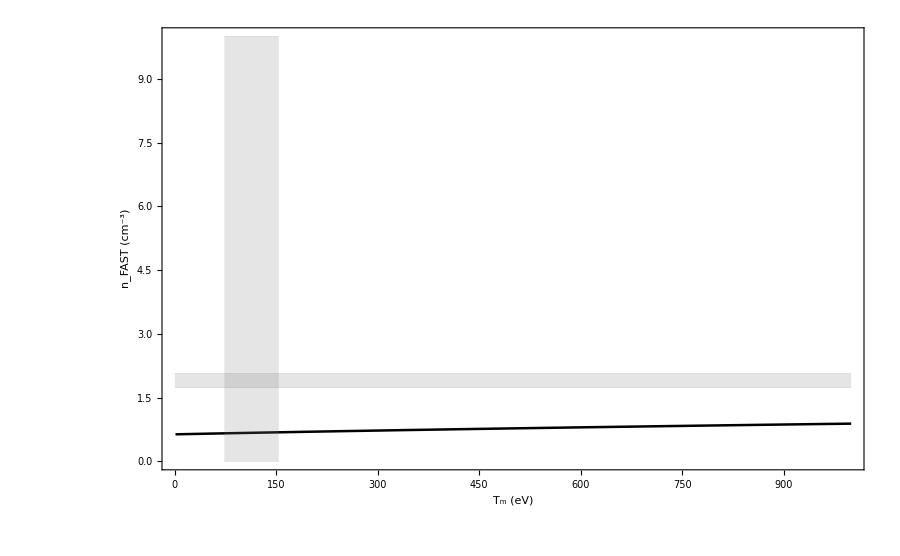

```mathematica
Show[Plot[funkerLiemohn[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{0,10}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```

## Just Maxwellian (resized)

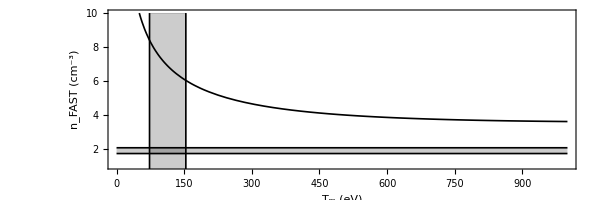

```mathematica
Show[Plot[funkerBarb[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,999},{1,10}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->{600,300},AspectRatio->1/3],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,10},{maxT,10}},{{minT,0},{minT,10}},{{maxT,0},{maxT,10}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->{Directive[Black,Thickness[0.002]],Directive[Black,Thickness[0.002]],Directive[Black,Thickness[0.0001]],Directive[Black,Thickness[0.0001]],Directive[Black,Thickness[0.002]],Directive[Black,Thickness[0.002]]}]]
```

## Maxwellian, with suggestive kappa lines

```mathematica
fakeKappa={1.53,1.6};
```

```mathematica
fakeStyles={Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]]};
```

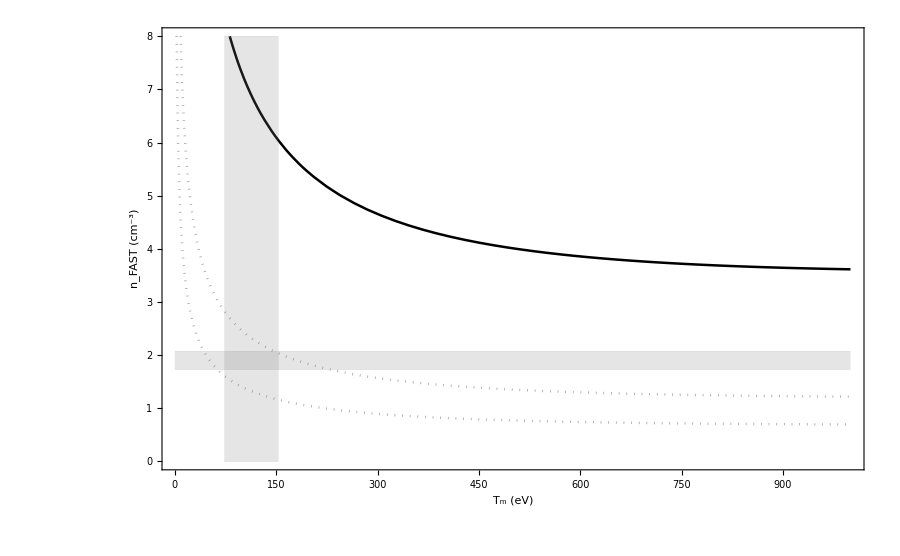

```mathematica
Show[Plot[funkerBarb[Ep,Tm,measCond],{Tm,1,1000},PlotStyle->styles[[8]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],Table[Plot[funkerFake[Ep,Tm,fakeKappa[[k]],measCond],{Tm,1,1000},PlotStyle->fakeStyles[[k]],PlotLegends->LineLegend[Automatic],PlotRange->{{1,1000},{0,8}},PlotRangeClipping->True,LabelStyle->(FontSize->19),Frame->True,FrameLabel->{StringForm["T_m (eV)"],StringForm["n_FAST (cm^-3)"]},FrameStyle->Directive[Black,19],ImageSize->900],{k,{1,2}}],ListLinePlot[{{{0,minDens},{1000,minDens}},{{0,maxDens},{1000,maxDens}},{{minT,0},{maxT,0}},{{minT,8},{maxT,8}}},Filling->{{1->{2}},{3->{4}}},PlotStyle->Directive[Gray,Thickness[0.0001]]]]
```